## The single-particle terms G_1 and G_2

```mathematica
ClearAll["Global`"]
```

```mathematica
test=N@(2Sqrt[3]*Sin[x+π/3]-Sqrt[3]*(Sqrt[3]*Cos[x]+Sin[x]))/.{x->π/5};
```

```mathematica
ftrig1[x_]:=2Sqrt[3]Sin[x+π/3];
ftrig2[x_]:=Sqrt[3](Sqrt[3]Cos[x]+Sin[x]);
```

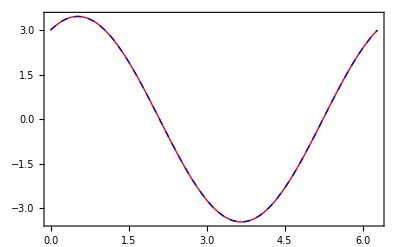

```mathematica
Plot[{ftrig1[x],ftrig2[x]},{x,0,2π},Frame->True,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}}]
```